```mathematica
a=-M/ve^2;
l=2rp-rp^2/a;
e=l/rp-1;

vp=Simplify[Sqrt[M(2/rp-1/a)]]
factor=Simplify[rp/vp]
```

√((2 M)/rp+ve^2)

rp/(√((2 M)/rp+ve^2))

```mathematica
nu=Simplify[ArcCos[(l-f rp)/(f rp e)]];
F=Simplify[ArcCosh[(e+Cos[nu])/(1+e Cos[nu])]];
t=Simplify[Sqrt[(-a)^3/M](e Sinh[F]-F), Assumptions->{M>0, rp>0, ve>0}]
```

(((-1+f) rp ve)/(√(((-1+f) rp)/(2 M+(1+f) rp ve^2)))-M ArcCosh[(M+f rp ve^2)/(M+rp ve^2)])/ve^3

```mathematica
g=Simplify[t/.{ve->1,rp->1}]
```

(-1+f)/(√((-1+f)/(1+f+2 M)))-M ArcCosh[(f+M)/(1+M)]

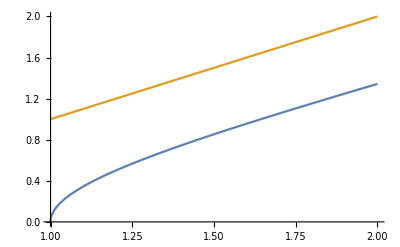

```mathematica
Plot[{g/.{ M->0.78},f},{f,1,2}]
```

```mathematica
Limit[D[g, f], f->Infinity]
```

1

```mathematica
Limit[D[g-f,f]f,f->Infinity]
```

-M

```mathematica
intercept=g-f+M Log[f];
int=Limit[intercept, f->Infinity, Assumptions->M>0]
```

M-M Log[2/(1+M)]

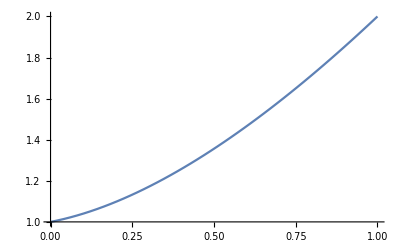

```mathematica
Plot[int+1,{M,0,1}]
```

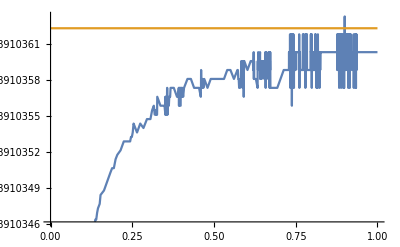

```mathematica
Plot[{intercept/.{ M->0.78}, int/.{ M->0.78}},{f,1,100000000}]
```

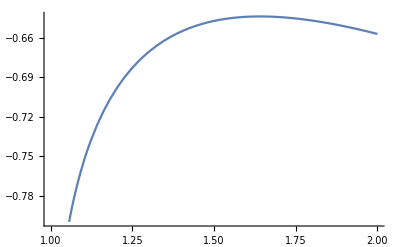

```mathematica
line=int+f-M Log[f];
Plot[{g-f/.{ M->0.78}},{f,1, 2}]
```

```mathematica
der=Simplify[D[g,f]-1]
```

-1+(f √((-1+f)/(1+f+2 M)))/(-1+f)

```mathematica
flinear=Solve[der==0,f, Assumptions->{M>0}][[1,1]]
```

f→(1+2 M)/(2 M)-(ⅈ √(1+2 M-2 (1+2 M)-(1+2 M)/(2 M)+(1+2 M)^2/(2 M)))/(√2 √M)

```mathematica
int=Simplify[( g-f)/.flinear]
```

((1+2 M) (-1+√(1/(1+2 M)^2)+2 M √(1/(1+2 M)^2)))/(2 M)-M ArcCosh[(1+2 M+2 M^2)/(2 M+2 M^2)]

0.356442

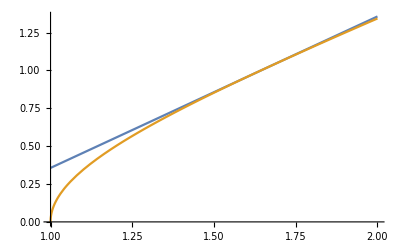

```mathematica
int+1/.M->0.78
Plot[{int+f/.M->.78, g/.M->0.78},{f,1,2}]
```

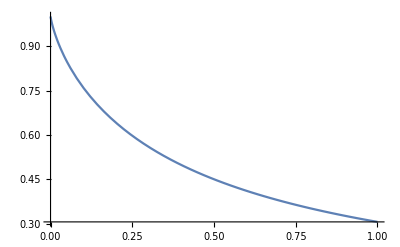

```mathematica
Plot[int+1,{M,0,1}]
```

```mathematica
(*The combination is (M/rpvp^2), and the plots you're seeing are how the times (variously defined) depend on M, which is a standin for this constant.*)
```

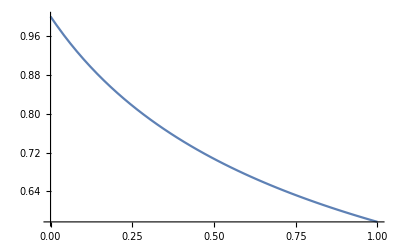

```mathematica
Plot[(2M+1)^(-1/2),{M,0,1}]
```

```mathematica
(5*6378000)/6000(2 *3.986004418*10^14/(6378000*6000^2)+1)^(-1/2)
```

2513.34

```mathematica
3.986004418*10^14/(6378000*6000^2)
```

1.736